# MakeZXDiagram

Make a diagrammatic representation of a linear map in the ZX-calculus

## Definition

```mathematica
GenerateZXGraph[zxExpression_]:=Module[{zSpiders,xSpiders,hadamardGates,diamonds,wires,graph,vertexSizes,emptyVertices},
zSpiders=First/@Cases[{zxExpression},_Z,Infinity,Heads->True];
xSpiders=First/@Cases[{zxExpression},_X,Infinity,Heads->True];
hadamardGates=First/@Cases[{zxExpression},_H,Infinity,Heads->True];
diamonds=First/@Cases[{zxExpression},_B,Infinity,Heads->True];
wires=Cases[{zxExpression},_W,Infinity,Heads->True]/.(W->DirectedEdge);
graph=Graph[Join[zSpiders,xSpiders,hadamardGates,diamonds],wires];
vertexSizes=(#->If[MemberQ[AdjacencyList[graph,#],#],0.01,0.4])&/@VertexList[graph];
emptyVertices=Complement[VertexList[graph],Join[zSpiders,xSpiders,hadamardGates,diamonds]];
Graph[Join[zSpiders,xSpiders,hadamardGates,diamonds],wires,VertexShapeFunction->Join[Thread[diamonds->"Diamond"],Thread[hadamardGates->"Square"]],VertexStyle->Join[Thread[zSpiders->Green],Thread[xSpiders->Red],Thread[hadamardGates->Yellow],Thread[diamonds->Black],Thread[emptyVertices->Directive[Transparent,EdgeForm[]]]],VertexSize->vertexSizes,GraphLayout->"SpringElectricalEmbedding",EdgeShapeFunction->GraphElementData["ShortFilledArrow","ArrowSize"->0.05]]]
GenerateZXGraphWithPhases[zxExpression_]:=Module[{zSpiders,zSpiderPhases,xSpiders,xSpiderPhases,hadamardGates,diamonds,wires,graph,vertexSizes,emptyVertices},
zSpiders=First/@Cases[{zxExpression},_Z,Infinity,Heads->True];
zSpiderPhases=Last/@Cases[{zxExpression},_Z,Infinity,Heads->True];
xSpiders=First/@Cases[{zxExpression},_X,Infinity,Heads->True];
xSpiderPhases=Last/@Cases[{zxExpression},_X,Infinity,Heads->True];
hadamardGates=First/@Cases[{zxExpression},_H,Infinity,Heads->True];
diamonds=First/@Cases[{zxExpression},_B,Infinity,Heads->True];
wires=Cases[{zxExpression},_W,Infinity,Heads->True]/.(W->DirectedEdge);
graph=Graph[Join[zSpiders,xSpiders,hadamardGates,diamonds],wires];
vertexSizes=(#->If[MemberQ[AdjacencyList[graph,#],#],0.01,0.4])&/@VertexList[graph];
emptyVertices=Complement[VertexList[graph],Join[zSpiders,xSpiders,hadamardGates,diamonds]];
Graph[Join[zSpiders,xSpiders,hadamardGates,diamonds],wires,VertexShapeFunction->Join[Thread[diamonds->"Diamond"],Thread[hadamardGates->"Square"]],VertexStyle->Join[Thread[zSpiders->Green],Thread[xSpiders->Red],Thread[hadamardGates->Yellow],Thread[diamonds->Black],Thread[emptyVertices->Directive[Transparent,EdgeForm[]]]],VertexLabels->Join[(First[#]->Placed[Last[#],Center]&/@Thread[zSpiders->zSpiderPhases]),(First[#]->Placed[Last[#],Center]&/@Thread[xSpiders->xSpiderPhases]),(#->Placed["H",Center])&/@hadamardGates],VertexSize->vertexSizes,VertexLabelStyle->Bold,GraphLayout->"SpringElectricalEmbedding",EdgeShapeFunction->GraphElementData["ShortFilledArrow","ArrowSize"->0.05]]]
zSpiderToMatrix[inputArity_Integer,outputArity_Integer,phase_]:=SparseArray[{{1,1}->1,{Power[2,outputArity],Power[2,inputArity]}->Exp[I*phase]}]
xSpiderToMatrix[inputArity_Integer,outputArity_Integer,phase_]:=Module[{antecedent,subsequent,hadamardGate},
hadamardGate=(1/Sqrt[2])*{{1,1},{1,-1}};
antecedent=Which[inputArity==0,IdentityMatrix[Power[2,inputArity]],inputArity==1,hadamardGate,inputArity≥2,Nest[KroneckerProduct[#,hadamardGate]&,KroneckerProduct[hadamardGate,hadamardGate],inputArity-2]];
subsequent=Which[outputArity==0,IdentityMatrix[Power[2,outputArity]],outputArity==1,hadamardGate,outputArity≥2,Nest[KroneckerProduct[#,hadamardGate]&,KroneckerProduct[hadamardGate,hadamardGate],outputArity-2]];
antecedent.SparseArray[{{1,1}->1,{Power[2,inputArity],Power[2,outputArity]}->Exp[I*phase]}].subsequent]
findLayers[graph_Graph]:=Module[{initialLayer,layers},
initialLayer=Select[VertexList[graph],VertexInDegree[graph,#]==0&];
If[Length[VertexList[graph]]>1,
layers=Association[Prepend[(#->Nest[DeleteDuplicates[Catenate[Module[{vertex=#},VertexOutComponent[graph,vertex,{1}]]&/@#]]&,initialLayer,#])&/@Range[Length[VertexList[graph]]],0->initialLayer]];
layers=Delete[layers,Position[Values[layers],i_/;Length[i]==0,{1},Heads->False]];
layers=Complement[#,Flatten[Join[Drop[Values[layers],Delete[Flatten[Position[Values[layers],#]],0]]]]]&/@layers,<||>]]
combineLayer[layer_List,matrixConversions_Association]:=Module[{generators},
generators=matrixConversions[#]&/@Intersection[layer,Keys[matrixConversions]];
Which[Length[generators]==1,SparseArray[generators[[1]]],Length[generators]>1,KroneckerProduct[Delete[generators,0]],Length[generators]==0,1]]
combineSubgraph[subgraph_Graph,matrixConversions_Association]:=Module[{layerMatrices,combinedSpiders,spidersToCombine,Ket0,Ket1,Bra0,Bra1},
layerMatrices=DeleteCases[combineLayer[#,matrixConversions]&/@Values[findLayers[subgraph]],_Integer];
Ket0=={{1},{0}};
Ket1={{0},{1}};
Bra0=ConjugateTranspose[Ket0];
Bra1=ConjugateTranspose[Ket1];
If[Length[layerMatrices]>0,
combinedSpiders=layerMatrices[[1]];
spidersToCombine=Rest[layerMatrices];
While[Length[spidersToCombine]>0,
combinedSpiders=Which[Dimensions[combinedSpiders][[2]]<Dimensions[spidersToCombine[[1]]][[1]],SparseArray[PadRight[#,Dimensions[spidersToCombine[[1]]][[1]]]&/@combinedSpiders].spidersToCombine[[1]],Dimensions[combinedSpiders][[2]]>Dimensions[spidersToCombine[[1]]][[1]],combinedSpiders.Join[spidersToCombine[[1]],Table[Table[0,Dimensions[spidersToCombine[[1]]][[2]]],(Dimensions[combinedSpiders][[2]]-Dimensions[spidersToCombine[[1]]][[1]])]],Dimensions[combinedSpiders][[2]]==Dimensions[spidersToCombine[[1]]][[1]],combinedSpiders.spidersToCombine[[1]],True,combinedSpiders];
spidersToCombine=Rest[spidersToCombine]],
combinedSpiders=Which[StringMatchQ[ToString[VertexList[subgraph][[1]]],"d"~~__],{Sqrt[2]},StringMatchQ[ToString[EdgeList[subgraph][[1,1]]],"i"~~__]&&StringMatchQ[ToString[EdgeList[subgraph][[1,2]]],"i"~~__]&&EdgeList[subgraph][[1,1]]=!=EdgeList[subgraph][[1,2]],KroneckerProduct[Bra0,Bra0]+KroneckerProduct[Bra1,Bra1],StringMatchQ[ToString[EdgeList[subgraph][[1,1]]],"o"~~__]&&StringMatchQ[ToString[EdgeList[subgraph][[1,2]]],"o"~~__]&&EdgeList[subgraph][[1,1]]=!=EdgeList[subgraph][[0,1]],KroneckerProduct[Ket0,Ket0]+KroneckerProduct[Ket1,Ket1],EdgeList[subgraph][[1,1]]==EdgeList[subgraph][[1,2]],{2},True,{1}]];
SparseArray[combinedSpiders]]
ConvertToMatrix[zxExpression_]:=Module[{hadamardGate,subgraphs,generatorsToMatrices,convertedSubgraphs},
hadamardGate=(1/Sqrt[2])*{{1,1},{1,-1}};
subgraphs=WeaklyConnectedGraphComponents[GenerateZXGraph[zxExpression]];
generatorsToMatrices=Association[Select[Flatten[zxExpression]/.CircleTimes->List,MemberQ[{X,Z,H,B},Head[#]]&]/.{X[xspider_,inputArity_Integer,outputArity_Integer,phase_]:>(xspider->xSpiderToMatrix[inputArity,outputArity,phase]),Z[zspider_,inputArity_Integer,outputArity_Integer,phase_]:>(zspider->zSpiderToMatrix[inputArity,outputArity,phase]),H[h_]:>(h->hadamardGate),B[d_]:>(d->Sqrt[2])}];
convertedSubgraphs=combineSubgraph[subgraphs[[#]],generatorsToMatrices]&/@Range[Length[subgraphs]];
If[Length[convertedSubgraphs]>1,KroneckerProduct[Delete[convertedSubgraphs,0]],convertedSubgraphs[[1]]]]
ZXDiagramObject/:MakeBoxes[diagram:ZXDiagramObject[zxExpression_],format_]:=Module[{icon,zSpiderCount,xSpiderCount,hadamardGateCount,diamondCount,wireCount},
zSpiderCount=Length[First/@Cases[{zxExpression},_Z,Infinity,Heads->True]];
xSpiderCount=Length[First/@Cases[{zxExpression},_X,Infinity,Heads->True]];
hadamardGateCount=Length[First/@Cases[{zxExpression},_H,Infinity,Heads->True]];
diamondCount=Length[First/@Cases[{zxExpression},_B,Infinity,Heads->True]];
wireCount=Length[Cases[{zxExpression},_W,Infinity,Heads->True]];
BoxForm`ArrangeSummaryBox["ZXDiagramObject",diagram,GenerateZXGraph[zxExpression],{{BoxForm`SummaryItem[{"Z Spiders: ",zSpiderCount}]},{BoxForm`SummaryItem[{"X Spiders: ",xSpiderCount}]},{BoxForm`SummaryItem[{"Hadamard Gates: ",hadamardGateCount}]}},{{BoxForm`SummaryItem[{"Diamonds: ",diamondCount}]},{BoxForm`SummaryItem[{"Wires: ",wireCount}]}},format,"Interpretable"->Automatic]]
ZXDiagramObject[zxExpression_]["OperatorForm"]:=zxExpression
ZXDiagramObject[zxExpression_]["ListForm"]:=Flatten[zxExpression]/.CircleTimes->List
ZXDiagramObject[zxExpression_]["MatrixForm"]:=Normal[ConvertToMatrix[zxExpression]]
ZXDiagramObject[zxExpression_]["ZSpiders"]:=Cases[{zxExpression},_Z,Infinity,Heads->True]
ZXDiagramObject[zxExpression_]["ZSpiderCount"]:=Length[Cases[{zxExpression},_Z,Infinity,Heads->True]]
ZXDiagramObject[zxExpression_]["XSpiders"]:=Cases[{zxExpression},_X,Infinity,Heads->True]
ZXDiagramObject[zxExpression_]["XSpiderCount"]:=Length[Cases[{zxExpression},_X,Infinity,Heads->True]]
ZXDiagramObject[zxExpression_]["HadamardGates"]:=Cases[{zxExpression},_H,Infinity,Heads->True]
ZXDiagramObject[zxExpression_]["HadamardGateCount"]:=Length[Cases[{zxExpression},_H,Infinity,Heads->True]]
ZXDiagramObject[zxExpression_]["Diamonds"]:=Cases[{zxExpression},_B,Infinity,Heads->True]
ZXDiagramObject[zxExpression_]["DiamondCount"]:=Length[Cases[{zxExpression},_B,Infinity,Heads->True]]
ZXDiagramObject[zxExpression_]["Wires"]:=Cases[{zxExpression},_W,Infinity,Heads->True]
ZXDiagramObject[zxExpression_]["WireCount"]:=Cases[{zxExpression},_W,Infinity,Heads->True]
ZXDiagramObject[zxExpression_]["UnlabeledGraph"]:=GenerateZXGraph[zxExpression]
ZXDiagramObject[zxExpression_]["LabeledGraph"]:=GenerateZXGraphWithPhases[zxExpression]
ZXDiagramObject[zxExpression_]["Properties"]:={"OperatorForm","ListForm","MatrixForm","ZSpiders","ZSpiderCount","XSpiders","XSpiderCount","HadamardGates","HadamardGateCount","Diamonds","DiamondCount","Wires","WireCount","UnlabeledGraph","LabeledGraph"}
MakeZXDiagram[components_List]:=Module[{oldComponents,operatorForm},
oldComponents=components;
operatorForm=oldComponents;
While[Length[oldComponents]>1,
operatorForm=operatorForm/.oldComponents->(CircleTimes[First[oldComponents],Rest[oldComponents]]);
oldComponents=Rest[oldComponents]];
operatorForm=(operatorForm/.oldComponents->First[oldComponents]);
ZXDiagramObject[operatorForm]]
MakeZXDiagram[<|"Diamonds"->diamondCount_Integer,"HadamardGates"->hadamardGateCount_Integer,"Wires"->wires_List,"XSpiders"->xSpiders_List,"ZSpiders"->zSpiders_List|>]:=Module[{validWires,zSpiderInputArities,zSpiderOutputArities,zSpiderPhases,zSpiderOperators,xSpiderInputArities,xSpiderOutputArities,xSpiderPhases,xSpiderOperators,hadamardGateOperators,diamondOperators,wireOperators},
validWires=False;
If[wires=!={},If[Length[Transpose[wires]]==2,validWires=True]];
If[wires==={},validWires=True];
If[validWires,
zSpiderInputArities=zSpiders[[1]];
zSpiderOutputArities=zSpiders[[2]];
zSpiderPhases=zSpiders[[3]];
zSpiderOperators=Table[Z[ToExpression["z"<>ToString[i]],zSpiderInputArities[[i]],zSpiderOutputArities[[i]],Which[NumberQ[zSpiderPhases[[i]]],Mod[zSpiderPhases[[i]],2*Pi],True,zSpiderPhases[[i]]]],{i,Length[zSpiderInputArities]}];
xSpiderInputArities=xSpiders[[1]];
xSpiderOutputArities=xSpiders[[2]];
xSpiderPhases=xSpiders[[3]];
xSpiderOperators=Table[X[ToExpression["x"<>ToString[i]],xSpiderInputArities[[i]],xSpiderOutputArities[[i]],Which[NumberQ[xSpiderPhases[[i]]],Mod[xSpiderPhases[[i]],2*Pi],True,xSpiderPhases[[i]]]],{i,Length[xSpiderInputArities]}];
hadamardGateOperators=Table[H[ToExpression["h"<>ToString[i]]],{i,hadamardGateCount}];
diamondOperators=Table[B[ToExpression["d"<>ToString[i]]],{i,diamondCount}];
wireOperators=Table[W[First[wires[[i]]],Last[wires[[i]]]],{i,Length[wires]}];
MakeZXDiagram[Join[zSpiderOperators,xSpiderOperators,hadamardGateOperators,diamondOperators,wireOperators]]]]/;(Length[zSpiders[[1]]]==Length[zSpiders[[2]]]&&Length[zSpiders[[2]]]==Length[zSpiders[[3]]]&&Length[xSpiders[[1]]]==Length[xSpiders[[2]]]&&Length[xSpiders[[2]]]==Length[xSpiders[[3]]])
MakeZXDiagram[assoc_Association,rest___]:=MakeZXDiagram[KeySortBy[assoc,Position[{"Diamonds","HadamardGates","Wires","XSpiders","ZSpiders"},#]&],rest]/;(Keys[assoc]≠{"Diamonds","HadamardGates","Wires","XSpiders","ZSpiders"}&&Sort[Keys[assoc]]=={"Diamonds","HadamardGates","Wires","XSpiders","ZSpiders"})
```

## Documentation

### Usage

MakeZXDiagram[gen]

makes a ZX-diagram using the list of generators gen.

MakeZXDiagram[assoc]

makes a ZX-diagram using the association of generators assoc.

### Details & Options

If MakeZXDiagram succeeds in constructing the specified ZX-diagram, then it returns a ZXDiagramObject expression.

Diagrammatic generators may be specified in List or Association form.

The following generator types are supported:

Z[name,in,out,phase] | a Z-spider with name name, input arity in, output arity out and phase phase
X[name,in,out,phase] | an X-spider with name name, input arity in, output arity out and phase phase
H[name] | a Hadamard gate with name name
B[name] | a black diamond with name name
W[name_1,name_2] | a wire connecting generators name_1 and name_2

When specified in Association form <|"ZSpiders"→z,"XSpiders"→x,"HadamardGates"→h,"Diamonds"→d,"Wires"→w|>, z and x are nested lists of input arities, output arities and phases; h and d are integers representing the number of Hadamard gates and black diamonds; and w is a nested list of generator names connected by wires.

In ZXDiagramObject, the following properties are supported:

"LabeledGraph" | graph form of the ZX-diagram with phases labeled
"UnlabeledGraph" | graph form of the ZX-diagram without phases labeled
"OperatorForm" | ZX-diagram represented as a tensor product of generators
"ListForm" | ZX-diagram represented as a list of generators
"MatrixForm" | ZX-diagram represented as an explicit linear map on qubits
"ZSpiders" | list of Z-spiders in the ZX-diagram
"XSpiders" | list of X-spiders in the ZX-diagram
"HadamardGates" | list of Hadamard gates in the ZX-diagram
"Diamonds" | list of black diamonds in the ZX-diagram
"Wires" | list of wires in the ZX-diagram
"ZSpiderCount" | number of Z-spiders in the ZX-diagram
"XSpiderCount" | number of X-spiders in the ZX-diagram
"HadamardGateCount" | number of Hadamard gates in the ZX-diagram
"DiamondCount" | number of black diamonds in the ZX-diagram
"WireCount" | number of wires in the ZX-diagram

The default convention is to name Z-spiders as z_1,z_2,…; X-spiders as x_1,x_2,…; Hadamard gates as h_1,h_2,…; black diamonds as d_1,d_2,…; inputs as i_1,i_2,…; and outputs as o_1,o_2,….

## Examples

### Basic Examples

Construct an elementary ZX-diagram corresponding to a simple unitary map:

```mathematica
diagram=MakeZXDiagram[{X[x,1,1,Pi/2],W[i,x],W[x,o]}]
```

ZXDiagramObject[…]

Show the labeled graph:

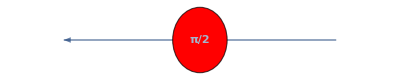

```mathematica
diagram["LabeledGraph"]
```

Show its operator form:

```mathematica
diagram["OperatorForm"]
```

X[x,1,1,π/2]⊗(W[i,x]⊗W[x,o])

Show its matrix form:

```mathematica
diagram["MatrixForm"]
```

{{1/2+ⅈ/2,1/2-ⅈ/2},{1/2-ⅈ/2,1/2+ⅈ/2}}

Construct a ZX-diagram from an association:

```mathematica
diagram=MakeZXDiagram[<|"ZSpiders"->{{2,2},{1,1},{Pi,Pi/2}},"XSpiders"->{{1,1},{2,2},{Pi/3,Pi/4}},"Wires"->{{i1,x1},{i2,x2},{x1,z1},{x1,z2},{x2,z1},{x2,z2},{z1,o1},{z2,o2}},"HadamardGates"->0,"Diamonds"->0|>]
```

ZXDiagramObject[…]

Show the unlabeled graph:

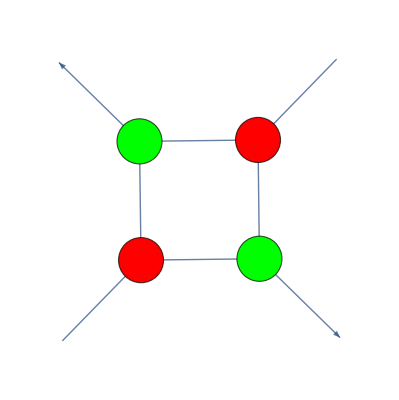

```mathematica
diagram["UnlabeledGraph"]
```

Show its operator form:

```mathematica
diagram["OperatorForm"]
```

Z[z1,2,1,π]⊗(Z[z2,2,1,π/2]⊗(X[x1,1,2,π/3]⊗(X[x2,1,2,π/4]⊗(W[i1,x1]⊗(W[i2,x2]⊗(W[x1,z1]⊗(W[x1,z2]⊗(W[x2,z1]⊗(W[x2,z2]⊗(W[z1,o1]⊗W[z2,o2]))))))))))

Show its matrix form:

```mathematica
diagram["MatrixForm"]
```

{{(1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)+ⅇ^((ⅈ π)/3)/(2 √2)),0,0,ⅈ (1/(2 √2)-ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)+ⅇ^((ⅈ π)/3)/(2 √2)),0,0,0,0,0,0,0,0,-(1/(2 √2)-ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)+ⅇ^((ⅈ π)/3)/(2 √2)),0,0,-ⅈ (1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)+ⅇ^((ⅈ π)/3)/(2 √2))},{(1/(2 √2)-ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)+ⅇ^((ⅈ π)/3)/(2 √2)),0,0,ⅈ (1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)+ⅇ^((ⅈ π)/3)/(2 √2)),0,0,0,0,0,0,0,0,-(1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)+ⅇ^((ⅈ π)/3)/(2 √2)),0,0,-ⅈ (1/(2 √2)-ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)+ⅇ^((ⅈ π)/3)/(2 √2))},{(1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)-ⅇ^((ⅈ π)/3)/(2 √2)),0,0,ⅈ (1/(2 √2)-ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)-ⅇ^((ⅈ π)/3)/(2 √2)),0,0,0,0,0,0,0,0,-(1/(2 √2)-ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)-ⅇ^((ⅈ π)/3)/(2 √2)),0,0,-ⅈ (1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)-ⅇ^((ⅈ π)/3)/(2 √2))},{(1/(2 √2)-ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)-ⅇ^((ⅈ π)/3)/(2 √2)),0,0,ⅈ (1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)-ⅇ^((ⅈ π)/3)/(2 √2)),0,0,0,0,0,0,0,0,-(1/(2 √2)+ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)-ⅇ^((ⅈ π)/3)/(2 √2)),0,0,-ⅈ (1/(2 √2)-ⅇ^((ⅈ π)/4)/(2 √2)) (1/(2 √2)-ⅇ^((ⅈ π)/3)/(2 √2))}}

Construct a more complicated ZX-diagram involving tensor products, Hadamard gates and diamonds:

```mathematica
diagram=MakeZXDiagram[{X[x1,0,1,Pi/2],Z[z1,3,4,0],Z[z2,2,1,0],X[x2,4,1,Pi/5],H[h1],Z[z3,0,1,Pi/3],X[x3,2,2,0],H[h2],W[x1,z1],W[i1,z1],W[i2,z1],W[z1,z2],W[z1,z2],W[z1,x2],W[z2,x2],W[z1,o1],W[i3,h1],W[h1,x2],W[z3,x2],W[x2,o4],B[d1],W[i4,h2],W[h2,x3],W[i5,x3],W[x3,o5],W[x3,o6]}]
```

ZXDiagramObject[…]

Show the unlabeled graph:

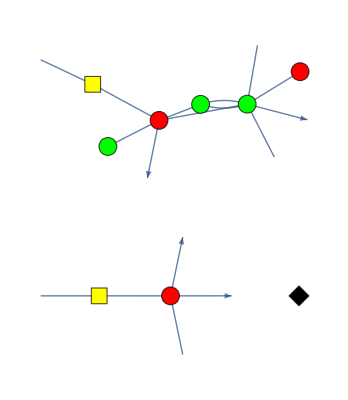

```mathematica
diagram["UnlabeledGraph"]
```

Show its operator form:

```mathematica
diagram["OperatorForm"]
```

X[x1,0,1,π/2]⊗(Z[z1,3,4,0]⊗(Z[z2,2,1,0]⊗(X[x2,4,1,π/5]⊗(H[h1]⊗(Z[z3,0,1,π/3]⊗(X[x3,2,2,0]⊗(H[h2]⊗(W[x1,z1]⊗(W[i1,z1]⊗(W[i2,z1]⊗(W[z1,z2]⊗(W[z1,z2]⊗(W[z1,x2]⊗(W[z2,x2]⊗(W[z1,o1]⊗(W[i3,h1]⊗(W[h1,x2]⊗(W[z3,x2]⊗(W[x2,o4]⊗(B[d1]⊗(W[i4,h2]⊗(W[h2,x3]⊗(W[i5,x3]⊗(W[x3,o5]⊗W[x3,o6]))))))))))))))))))))))))

Show its matrix form:

```mathematica
diagram["MatrixForm"]
```

{{(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2))},{(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2))},{(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2))},{(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2))}}

### Scope

#### ZX generators

All of the standard generators of the ZX-calculus are supported (for both the computational and Hadamard-transformed bases), including states:

```mathematica
diagram1=MakeZXDiagram[{Z[z,0,1,α],W[z,o]}]
```

ZXDiagramObject[…]

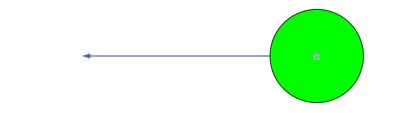

```mathematica
diagram1["LabeledGraph"]
```

```mathematica
diagram1["MatrixForm"]
```

{{1},{ⅇ^(ⅈ α)}}

```mathematica
diagram2=MakeZXDiagram[{X[x,0,1,α],W[x,0]}]
```

ZXDiagramObject[…]

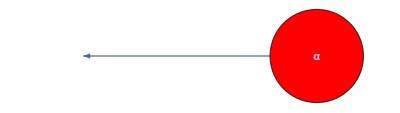

```mathematica
diagram2["LabeledGraph"]
```

```mathematica
diagram2["MatrixForm"]
```

{{1/(√2)+ⅇ^(ⅈ α)/(√2),1/(√2)-ⅇ^(ⅈ α)/(√2)}}

Unitary maps:

```mathematica
diagram1=MakeZXDiagram[{Z[z,1,1,α],W[i,z],W[z,o]}]
```

ZXDiagramObject[…]

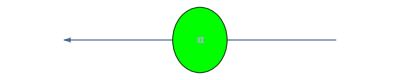

```mathematica
diagram1["LabeledGraph"]
```

```mathematica
diagram1["MatrixForm"]
```

{{1,0},{0,ⅇ^(ⅈ α)}}

```mathematica
diagram2=MakeZXDiagram[{X[x,1,1,α],W[i,x],W[x,o]}]
```

ZXDiagramObject[…]

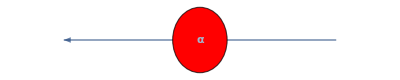

```mathematica
diagram2["LabeledGraph"]
```

```mathematica
diagram2["MatrixForm"]
```

{{1/2+ⅇ^(ⅈ α)/2,1/2-ⅇ^(ⅈ α)/2},{1/2-ⅇ^(ⅈ α)/2,1/2+ⅇ^(ⅈ α)/2}}

Linear isometries:

```mathematica
diagram1=MakeZXDiagram[{Z[z,1,2,α],W[i,z],W[z,o1],W[z,o2]}]
```

ZXDiagramObject[…]

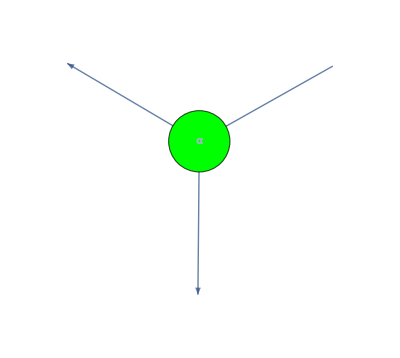

```mathematica
diagram1["LabeledGraph"]
```

```mathematica
diagram1["MatrixForm"]
```

{{1,0},{0,0},{0,0},{0,ⅇ^(ⅈ α)}}

```mathematica
diagram2=MakeZXDiagram[{X[x,1,2,α],W[i,x],W[x,o1],W[x,o2]}]
```

ZXDiagramObject[…]

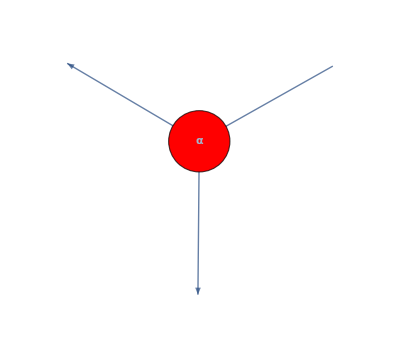

```mathematica
diagram2["LabeledGraph"]
```

```mathematica
diagram2["MatrixForm"]
```

{{1/(2 √2)+ⅇ^(ⅈ α)/(2 √2),1/(2 √2)-ⅇ^(ⅈ α)/(2 √2),1/(2 √2)-ⅇ^(ⅈ α)/(2 √2),1/(2 √2)+ⅇ^(ⅈ α)/(2 √2)},{1/(2 √2)-ⅇ^(ⅈ α)/(2 √2),1/(2 √2)+ⅇ^(ⅈ α)/(2 √2),1/(2 √2)+ⅇ^(ⅈ α)/(2 √2),1/(2 √2)-ⅇ^(ⅈ α)/(2 √2)}}

Partial linear isometries:

```mathematica
diagram1=MakeZXDiagram[{Z[z,2,1,α],W[i1,z],W[i2,z],W[z,o]}]
```

ZXDiagramObject[…]

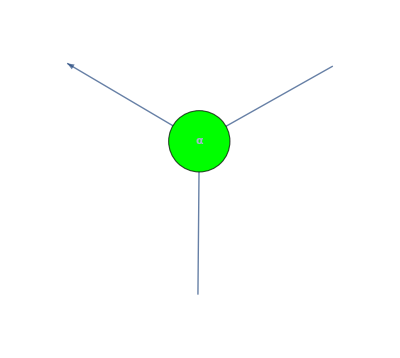

```mathematica
diagram1["LabeledGraph"]
```

```mathematica
diagram1["MatrixForm"]
```

{{1,0,0,0},{0,0,0,ⅇ^(ⅈ α)}}

```mathematica
diagram2=MakeZXDiagram[{X[x,2,1,α],W[i1,x],W[i2,x],W[x,o]}]
```

ZXDiagramObject[…]

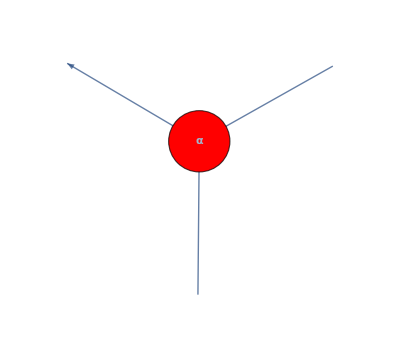

```mathematica
diagram2["LabeledGraph"]
```

```mathematica
diagram2["MatrixForm"]
```

{{1/(2 √2)+ⅇ^(ⅈ α)/(2 √2),1/(2 √2)-ⅇ^(ⅈ α)/(2 √2)},{1/(2 √2)-ⅇ^(ⅈ α)/(2 √2),1/(2 √2)+ⅇ^(ⅈ α)/(2 √2)},{1/(2 √2)-ⅇ^(ⅈ α)/(2 √2),1/(2 √2)+ⅇ^(ⅈ α)/(2 √2)},{1/(2 √2)+ⅇ^(ⅈ α)/(2 √2),1/(2 √2)-ⅇ^(ⅈ α)/(2 √2)}}

Projections (i.e. projective measurements):

```mathematica
diagram1=MakeZXDiagram[{Z[z,0,1,α],W[i,z]}]
```

ZXDiagramObject[…]

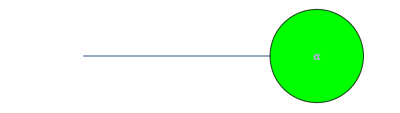

```mathematica
diagram1["LabeledGraph"]
```

```mathematica
diagram1["MatrixForm"]
```

{{1},{ⅇ^(ⅈ α)}}

```mathematica
diagram2=MakeZXDiagram[{X[x,0,1,α],W[i,x]}]
```

ZXDiagramObject[…]

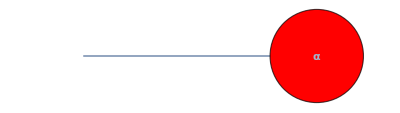

```mathematica
diagram2["LabeledGraph"]
```

```mathematica
diagram2["MatrixForm"]
```

{{1/(√2)+ⅇ^(ⅈ α)/(√2),1/(√2)-ⅇ^(ⅈ α)/(√2)}}

Hadamard gates:

```mathematica
diagram=MakeZXDiagram[{H[h],W[i,h],W[h,o]}]
```

ZXDiagramObject[…]

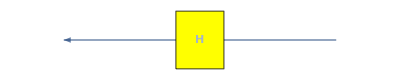

```mathematica
diagram["LabeledGraph"]
```

```mathematica
diagram["MatrixForm"]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

Black diamonds (i.e. scalar factors):

```mathematica
diagram=MakeZXDiagram[{B[d]}]
```

ZXDiagramObject[…]

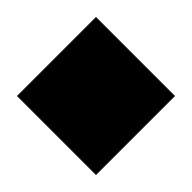

```mathematica
diagram["UnlabeledGraph"]
```

#### ZX-diagram properties

Properties supported by ZXDiagramObject include labeled graphs:

```mathematica
diagram=MakeZXDiagram[{X[x1,0,1,Pi/2],Z[z1,3,4,0],Z[z2,2,1,0],X[x2,4,1,Pi/5],H[h1],Z[z3,0,1,Pi/3],X[x3,2,2,0],H[h2],W[x1,z1],W[i1,z1],W[i2,z1],W[z1,z2],W[z1,z2],W[z1,x2],W[z2,x2],W[z1,o1],W[i3,h1],W[h1,x2],W[z3,x2],W[x2,o4],B[d1],W[i4,h2],W[h2,x3],W[i5,x3],W[x3,o5],W[x3,o6]}]
```

ZXDiagramObject[…]

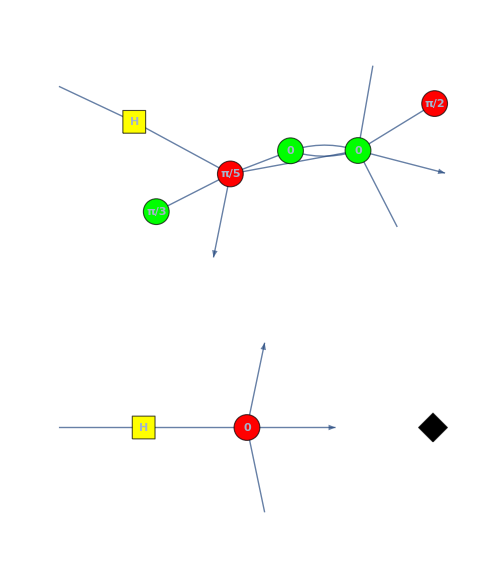

```mathematica
diagram["LabeledGraph"]
```

Unlabeled graphs:

```mathematica
diagram["UnlabeledGraph"]
```

-Graphics-

Operator forms:

```mathematica
diagram["OperatorForm"]
```

X[x1,0,1,π/2]⊗(Z[z1,3,4,0]⊗(Z[z2,2,1,0]⊗(X[x2,4,1,π/5]⊗(H[h1]⊗(Z[z3,0,1,π/3]⊗(X[x3,2,2,0]⊗(H[h2]⊗(W[x1,z1]⊗(W[i1,z1]⊗(W[i2,z1]⊗(W[z1,z2]⊗(W[z1,z2]⊗(W[z1,x2]⊗(W[z2,x2]⊗(W[z1,o1]⊗(W[i3,h1]⊗(W[h1,x2]⊗(W[z3,x2]⊗(W[x2,o4]⊗(B[d1]⊗(W[i4,h2]⊗(W[h2,x3]⊗(W[i5,x3]⊗(W[x3,o5]⊗W[x3,o6]))))))))))))))))))))))))

List forms:

```mathematica
diagram["ListForm"]
```

{X[x1,0,1,π/2],Z[z1,3,4,0],Z[z2,2,1,0],X[x2,4,1,π/5],H[h1],Z[z3,0,1,π/3],X[x3,2,2,0],H[h2],W[x1,z1],W[i1,z1],W[i2,z1],W[z1,z2],W[z1,z2],W[z1,x2],W[z2,x2],W[z1,o1],W[i3,h1],W[h1,x2],W[z3,x2],W[x2,o4],B[d1],W[i4,h2],W[h2,x3],W[i5,x3],W[x3,o5],W[x3,o6]}

Matrix forms:

```mathematica
diagram["MatrixForm"]
```

{{(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2))},{(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2))},{(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2))},{(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)+ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(-1/4-ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2)),(1/4+ⅈ/4) ⅇ^((ⅈ π)/3) (1/(4 √2)-ⅇ^((ⅈ π)/5)/(4 √2))}}

Z-spider lists:

```mathematica
diagram["ZSpiders"]
```

{Z[z1,3,4,0],Z[z2,2,1,0],Z[z3,0,1,π/3]}

X-spider lists:

```mathematica
diagram["XSpiders"]
```

{X[x1,0,1,π/2],X[x2,4,1,π/5],X[x3,2,2,0]}

Hadamard gate lists:

```mathematica
diagram["HadamardGates"]
```

{H[h1],H[h2]}

Black diamond lists:

```mathematica
diagram["Diamonds"]
```

{B[d1]}

Wire lists:

```mathematica
diagram["Wires"]
```

{W[x1,z1],W[i1,z1],W[i2,z1],W[z1,z2],W[z1,z2],W[z1,x2],W[z2,x2],W[z1,o1],W[i3,h1],W[h1,x2],W[z3,x2],W[x2,o4],W[i4,h2],W[h2,x3],W[i5,x3],W[x3,o5],W[x3,o6]}

## Source & Additional Information

### Contributed By

Jonathan Gorard and Manojna Namuduri (with additional contributions by Xerxes Arsiwalla)

### Keywords

Fundamental physics

Category theory

Mathematical logic

Quantum mechanics

Quantum information theory

Quantum computing

Abstract rewriting

Automated theorem-proving

### Categories

3D Visualization |  Accessibility
 Accessing External Services & APIs |  Associations
 Astronomical Computation & Data |  Background & Scheduled Tasks
 Calculus |  Calling External Programs
 Cloud & Deployment |  Cloud Functions & Deployment
 Code as Data |  Color Processing
 Computational Geometry |  Computation on Graphs
 Computer Vision |  Control Objects
 Core Language & Structure |  Creating Form Interfaces & Apps
 Cryptography |  Cultural Data
 Data Manipulation & Analysis |  Data Structures
 Data Transforms and Smoothing |  Data Visualization
 Date & Time |  Decorations
 Differential Geometry |  Dimension Reduction
 Discrete Mathematics |  Dynamic Interactivity Language
 Engineering Data & Computation |  Error Handling
 Expressions |  External Interfaces & Connections
 External Language Interfaces |  File Operations
 Financial Data & Computation |  Front End Utilities
 Functional Programming |  Function Visualization
 Games |  Geographic Data and Entities
 Geographic Data & Computation |  Geographic Visualization
 Geometric Region Properties |  Geometric Transforms
 Geometry |  Graph Construction & Representation
 Graph Properties & Measurements |  Graphs & Networks
 Graph Visualization |  Handling Arrays of Data
 Higher Mathematical Computation |  Image Filtering & Neighborhood Processing
 Image Processing & Analysis |  Images
 Importing and Exporting |  Interactive Manipulation
 Iterated Maps & Fractals |  Just For Fun
 Knowledge Representation & Natural Language |  Layout & Tables
 Life Sciences & Medicine: Data & Computation |  Linguistic Data
 List Manipulation |  Logic & Boolean Algebra
 Low-Level Notebook Programming |  Machine Learning
 Maps & Cartography |  Mathematical Functions
 Matrices and Linear Algebra |  Molecular Structure & Computation
 Natural Language Processing |  Neural Networks
 Notebook Basics |  Notebook Document Generation
 Notebook Documents & Presentation |  Notebook Formatting & Styling
 Number Theory |  Numeric Approximation
 Optimization |  Parallel Computing
 Persistent Storage |  Physics & Chemistry: Data and Computation
 Plane Geometry |  Polynomial Algebra
 Precollege Education |  Presentations with the Wolfram System
 Probability & Statistics |  Programming Utilities
 Random Stuff |  Real & Complex Analysis
 Recreational Math |  Repository Tools
 RepositoryTools |  Rules & Patterns
 Scientific and Medical Data & Computation |  Scientific Data Analysis
 Segmentation Analysis |  Sequence Analysis
 Shortcuts and Idioms |  Signal Processing
 Social, Cultural & Linguistic Data |  Social Data
 Solid Geometry |  Sound & Video
 Statistical Data Analysis |  String Manipulation
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Text Analysis
 Text Manipulation |  Theorem Proving
 Time-Related Computation |  Time Series Processing
 Topology |  Tuning & Debugging
 Units & Quantities |  User Interface Construction
 Viewers and Annotation |  Visualization & Graphics
 Weather Data |  Web Operations
 Wolfram Physics Project |  Wolfram System Setup
 Working with Paclets |

### Related Symbols

FindEquationalProof

### Related Resource Objects

MultiwaySystem

MultiwayOperatorSystem

BranchPairs

BranchPairResolutions

CanonicalBranchPairs

CausalInvariantQ

TotalCausalInvariantQ

KnuthBendixCompletion

CanonicalKnuthBendixCompletion

### Source/Reference Citation

Bob Coecke and Ross Duncan (2011), "Interacting Quantum Observables: Categorical Algebra and Diagrammatics"

Stephen Wolfram (2002), A New Kind of Science

Stephen Wolfram (2020), "A Class of Models with the Potential to Represent Fundamental Physics"

Jonathan Gorard (2020), "Some Relativistic and Gravitational Properties of the Wolfram Model"

Jonathan Gorard (2020), "Some Quantum Mechanical Properties of the Wolfram Model"

### Links

The ZX-calculus

The Wolfram Physics Project

Stephen Wolfram's A New Kind of Science | Online

Multiway System–Wolfram MathWorld

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.